To load the functionality for verifying operator identities via noncommutative Groebner basis computations, just load the OperatorGB package. This can be done by the following command:

```mathematica
<<"/Users/clemenshofstadler/Desktop/Project/OperatorGB.m"
```

Package OperatorGB version 1.0.0
Copyright 2019, Institute of Algebra, JKU
written by Clemens Hofstadler

A few definitions need to be made by the user. Type ?SetUpRing, ?Weight for more information.

We will illustrate the functionality of the package and its usage on a concrete example. Therefore, we assume that we are given two linear operators A and B, with A having codomain V and domain W and B having codomain U and domain V. Furthermore, we are given inner inverses of A and B denoted by A^- and B^-, respectively, i.e. operators satisfying AA^-A = A and BB^-B = B.

We want to prove the reverse order law which, in this case, reads as follows:

							ABB^-A^-AB = AB.
							
To prove this statement, we will need an additional assumption on A, B, A^- and B^-, which is that the operator A^-ABB^- is idempotent. This means A^-ABB^-A^-ABB^-=A^-ABB^-.

To prove such operator identities, the equations first have to be translated  into (noncommutative) polynomials. To do this, the user has to set up a corresponding noncommutative polynomial ring first. This is done by providing a list of all variables that the ring shall contain. For our example, we will set up a noncommutative polynomial ring in the variables  a,a^-,b,b^-.

```mathematica
SetUpRing[{a,SuperMinus[a],b,SuperMinus[b]}]
```

a < a^- < b < b^-

The monomial order in this polynomial ring is predefined to be graded lexicographic, where the variables are ordered in ascending order corresponding to the input list of the SetUpRing method. Hence, in our case, we get  a<a^-<b<b^-.

The user has the option to change the monomial order. The second pre-defined order is a weighted graded lexicographic order. To switch to this order, the user has execute the command

```mathematica
SortedQ = WeightedDegLex;
```

Then, additionally, a list of weights {w1,w2,...} named Weight has to be provided, where w1 corresponds to the weight of the first variable in the input list of SetUpRing, w2 to the second one and so on.

```mathematica
Weight = {5,5,1,3};
```

To define an individual order, the user can provide a binary function SortedQ[a,b] working on the set of all words that can be built from the alphabet of variables. It decides, when given two words as input, which of them is larger. For now, however, we will stick to the degree lexicographic order.

```mathematica
SortedQ = DegLex;
```

An ideal can be defined simply by providing the generators as polynomials using the built in noncommutative multiplication. For our example, our ideal contains all our assumptions, i.e. the equations that A, A^-, B and B^- satisfy translated into noncommutative polynomials.

```mathematica
assumptions = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
```

Note that to be able to obtain a cofactor representation w.r.t the assumptions, all generators of this ideal have to be monic. Otherwise, only a cofactor representation w.r.t. to monic versions of the generators is computed.

To now compute a Groebner basis of the ideal generated by our assumptions, the user has to provide a name. In a list with this given name the cofactors of the new elements of the Groebner basis will be saved. 
We will provide the name “cofactors”.

The Groebner basis can then be computed using the method
Groebner[cofactors,ideal,maxiter,MaxDeg->Infinity,Info->False,Parallel->True,Sorted->False].
An additional parameter maxiter can be provided to determine how many iterations of the Buchberger algorithm are executed at most. By default this value is set to 10. It is also possible to set the OptionPattern MaxDeg (default: Infinity) which determines the maximal degree of ambiguities that are considered during the Groebner basis computation (ambiguities with larger degree are simply ignored). Another OptionPattern is Info which can be set to True (default False) to receive information about the computation progress. Furthermore, the OptionPattern Parallel allows the user to specify whether all possible computations are executed in parallel or all computations are executed in series (default True). The OptionPattern Sorted sorts the ambiguities before processing if set to True (default False). This might speed up the computation but when only a partial Groebner basis is computed, this results in a different partial Groebner basis then the result when executing the same computation with Sorted disabled. 

To compute a (partial) Groebner basis of an ideal without computing the cofactors, the method 
GroebnerWithoutCofactors[ideal, maxiter,MaxDeg->Infinity, Info->False, Parallel->True, Sorted->False,  Criterion->False] can be used. It is slightly faster than Groebner. For further information see the documentation of the source code.

For our example, we will now compute a Groebner basis of the ideal generated by our assumptions together with the corresponding cofactors:

```mathematica
G = Groebner[cofactors,assumptions,Info->True];
```

G has 3 elements in the beginning.

5 ambiguities in total (computation took 0.000461)

Generating S-polys: 1.81284

Reducing S-polys: 0.000208

2 different S-polynomials did not reduce to 0 (computation took 1.81357)

The reduction took 0.155234

Iteration 1 finished. G has now 5 elements

15 ambiguities in total (computation took 0.009045)

Generating S-polys: 0.021329

Reducing S-polys: 0.000355

2 different S-polynomials did not reduce to 0 (computation took 0.022359)

The reduction took 0.201209

Iteration 2 finished. G has now 6 elements

12 ambiguities in total (computation took 0.0097)

Generating S-polys: 0.010665

Reducing S-polys: 0.000235

0 different S-polynomials did not reduce to 0 (computation took 0.01166)

Rewriting the cofactors has started.

Rewriting the cofactors took in total 0.002276

G now contains a Groebner basis of the ideal:

```mathematica
G
```

{-a+a**a^-**a,-b+b**b^-**b,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,-a**b**b^-+a**b**b^-**a^-**a**b**b^-,-a^-**a**b+a^-**a**b**b^-**a^-**a**b,-a**b+a**b**b^-**a^-**a**b}

During the Groebner basis computation a list named “cofactors” has been generated. For each element g that has been added to the Groebner basis, this list contains a pair {g,l}, where l is a list of triples {a,f,b}. This list of triples forms a linear combination of g in terms of the monic generators f of the ideal and certain cofactors a,b.

```mathematica
cofactors
```

{{-a**b**b^-+a**b**b^-**a^-**a**b**b^-,{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}}},{-a^-**a**b+a^-**a**b**b^-**a^-**a**b,{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}}},{-a**b+a**b**b^-**a^-**a**b,{{a**a^-**a,-b+b**b^-**b,1},{-a**a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b},{1,-a+a**a^-**a,b}}}}

The first pair {g,l} in cofactors corresponds to the first element that has been added to the Groebner basis, i.e to G[[4]] = -abb^-+abb^-a^-abb.

```mathematica
cofactors[[1,1]]
```

-a**b**b^-+a**b**b^-**a^-**a**b**b^-

```mathematica
cofactors[[1,2]]
```

{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}}

Actually computing this linear combination yields

```mathematica
MultiplyOut[cofactors[[1,2]]]
```

-a**b**b^-+a**b**b^-**a^-**a**b**b^-

We can prove our claim (the reverse order law) by testing whether the polynomial corresponding to this operator identity lies in the ideal generated by our assumptions. This ideal membership can be tested using the method ReducedForm[vars,G,exp], which reduces the expression exp using the elements of G and saves the linear combination obtained by these reduction steps in a list named “vars”.

So, we transform our claim into a polynomial...

```mathematica
claim= a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
```

...and show that this polynomial can be reduced to 0 using our Groebner basis G.

```mathematica
ReducedForm[vars,G,claim]
```

0

And we also obtain a linear combination of the claim in terms of the elements of G

```mathematica
MultiplyOut[vars]
```

-a**b+a**b**b^-**a^-**a**b

Usually, we want to have a linear combination only consisting of the generators of the ideal, i.e. of our assumptions. This can be achieved using the method Rewrite[vars,cofactors], where cofactors is the list obtained from calling MyGroebner[cofactors,assumptions].

```mathematica
Rewrite[vars,cofactors]
```

{{a**a^-**a,-b+b**b^-**b,1},{-a**a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b},{1,-a+a**a^-**a,b}}

The resulting list consists only of triples {a,f,b}, where a,b are certain cofactors and f are the monic generators of the ideal. We can check that this list still yields the same result when we compute the linear combination:

```mathematica
MultiplyOut[%] === claim
```

True

Additionally, the package also allows to work with labelled quivers (not necessarily with unique labels). Such a quiver can be defined by providing a list of triples {l,s,t}, where l is the label, s is the source and t the target of a certain edge in the quiver. We can set up a quiver for our example as follows:

```mathematica
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
```

To get a better overview, we can plot the quiver:

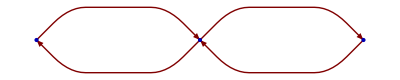

```mathematica
PlotQuiver[Q]
```

And we can check whether our assumptions and the claim are compatible with this quiver using the function QSignature. This ensures that if we obtain a successful proof without checking compatibility at every step, then there also exists a (maybe different) proof that uses only compatible expressions.

```mathematica
QSignature[assumptions,Q]
```

{{{V,W}},{{U,V}},{{V,V}}}

```mathematica
QSignature[claim,Q]
```

{{U,W}}

The result of this function is the signature of each of the input polynomials given as a list of pairs. In the case of the zero polynomial (for which no signature is defined), a list of all empty paths is returned. If this signature is not empty, the polynomial is compatible with the corresponding quiver.

All of the computations described above can also be done all at once by calling the method Certify[assumptions, claims, Q], which takes some assumptions, one or more claims and a quiver Q and then first of all determines whether the assumptions and claims are indeed compatible with Q. If this is the case,  a Groebner basis is computed, the claims are reduced with this Groebner basis and the reduced claims as well as a linear combination of the claims in terms of the (monic) assumptions is returned. Hence, we can replicate all the computations that we have done so far with the command

```mathematica
Certify[assumptions,claim,Q,Info->True]
```

Using the following monomial ordering:

a < a^- < b < b^-

Computing a (partial) Groebner basis...

G has 3 elements in the beginning.

5 ambiguities in total (computation took 0.000451)

Generating S-polys: 0.00857

Reducing S-polys: 0.000217

2 different S-polynomials did not reduce to 0 (computation took 0.009323)

The reduction took 0.253499

Iteration 1 finished. G has now 5 elements

15 ambiguities in total (computation took 0.008652)

Generating S-polys: 0.009936

Reducing S-polys: 0.000438

2 different S-polynomials did not reduce to 0 (computation took 0.010977)

The reduction took 0.162179

Iteration 2 finished. G has now 6 elements

12 ambiguities in total (computation took 0.008103)

Generating S-polys: 0.009762

Reducing S-polys: 0.000189

0 different S-polynomials did not reduce to 0 (computation took 0.010636)

Rewriting the cofactors has started.

Rewriting the cofactors took in total 0.00214

Reducing the claim with the Groebner basis and rewriting the linear combination in terms of the assumptions has started...

{{{{V,W}},{{U,V}},{{V,V}}},{{U,W}},0,{{a**a^-**a,-b+b**b^-**b,1},{-a**a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b},{1,-a+a**a^-**a,b}}}

And, similarly as before we see that the claim can be reduced to 0 and multiplying out the linear combinations yields

```mathematica
MultiplyOut[%[[4]]]===claim
```

True